# Genetic programming

## Expression representation

```mathematica
GetLabelName[label_]:=Replace[label,Framed[Style[labelName_,___],___]:>labelName];

FunctionToGraph[expr_]:=Block[{tree,labels,functionNames,terminalNames,vertexLabels,order,pos},
tree = ToExpression@ToBoxes@TreeForm[expr];
labels=Cases[tree,Inset[name_,n_]:>Rule[n,GetLabelName[name]],Infinity] /.HoldForm[f_]:>f;
functionNames = DeleteDuplicates@Cases[expr,f_[_,_]:>f,All];
terminalNames = Complement[DeleteDuplicates[labels[[All,2]]],functionNames];
vertexLabels = labels /.Join[Thread[functionNames->Map[Func,functionNames]], Thread[terminalNames->Map[Term,terminalNames]]];

{order,pos}=Catenate/@Cases[tree,Line[order_]|GraphicsComplex[pos_,___]:>{order,pos},Infinity];
{Graph[DirectedEdge@@@order,VertexLabels->labels],vertexLabels}
];
GraphToFunction[edgeList_,vertexLabels_]:=Block[{depthFirstScan},
depthFirstScan = Reverse@First@Last@Reap@DepthFirstScan[edgeList,1,{"PostvisitVertex"->(Sow[#]&)}] /. vertexLabels;

First@FixedPoint[SequenceReplace[#,{Func[f_],Term[x_],Term[y_]}:>Term[f[x,y]]]&,depthFirstScan]/.Term[x_]:>x
];
```

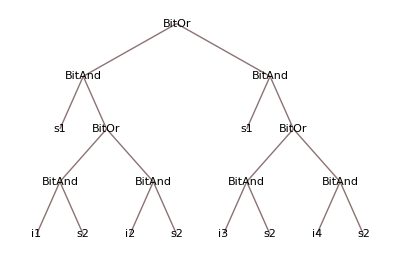

```mathematica
TreeForm[BitOr[BitAnd[s1,BitOr[BitAnd[i3,s2],BitAnd[i4,s2]]],BitAnd[s1,BitOr[BitAnd[i1,s2],BitAnd[i2,s2]]]]]
```

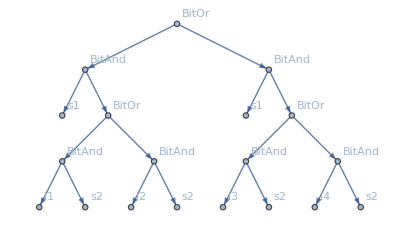
{-Graphics-,{1→Func[BitOr],2→Func[BitAnd],3→Term[s1],4→Func[BitOr],5→Func[BitAnd],6→Term[i1],7→Term[s2],8→Func[BitAnd],9→Term[i2],10→Term[s2],11→Func[BitAnd],12→Term[s1],13→Func[BitOr],14→Func[BitAnd],15→Term[i3],16→Term[s2],17→Func[BitAnd],18→Term[i4],19→Term[s2]}}

```mathematica
FunctionToGraph[BitOr[BitAnd[s1,BitOr[BitAnd[i1,s2],BitAnd[i2,s2]]],BitAnd[s1,BitOr[BitAnd[i3,s2],BitAnd[i4,s2]]]]]
```

```mathematica
GraphToFunction[
-Graphics-,
{1->Func[BitOr],2->Func[BitAnd],3->Term[s1],4->Func[BitOr],5->Func[BitAnd],6->Term[i1],7->Term[s2],8->Func[BitAnd],9->Term[i2],10->Term[s2],11->Func[BitAnd],12->Term[s1],13->Func[BitOr],14->Func[BitAnd],15->Term[i3],16->Term[s2],17->Func[BitAnd],18->Term[i4],19->Term[s2]}
]
```

BitOr[BitAnd[s1,BitOr[BitAnd[i1,s2],BitAnd[i2,s2]]],BitAnd[s1,BitOr[BitAnd[i3,s2],BitAnd[i4,s2]]]]

## Operations on trees

```mathematica
Subtree[graph_,vertex_,labels_]:=Block[{children,toDelete,subtree,sublabels},
children = First@Last@Reap@DepthFirstScan[graph,vertex,{"PrevisitVertex"->(Sow[#]&)}];
toDelete = Complement[VertexList[graph],children];
subtree = VertexDelete[graph,Complement[VertexList[graph],children]];
sublabels = Cases[labels,x_/;MemberQ[children,First[x]]];

{subtree,sublabels}
];
```

```mathematica
f1 = BitOr[BitAnd[s1,BitOr[BitAnd[i3,s2],BitAnd[i4,s2]]],BitAnd[s1,BitOr[BitAnd[i1,s2],BitAnd[i2,s2]]]];
f2 = BitOr[BitAnd[s1,BitOr[BitOr[i3,s2],BitAnd[i4,s2]]],BitXor[s1,s2]];
```

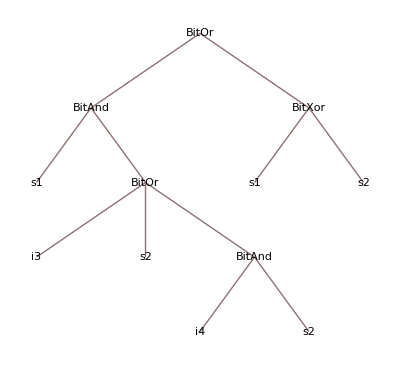
{-Graphics-,-Graphics-}

```mathematica
Map[TreeForm,{f1,f2}]
```

```mathematica
{g1,l1} = FunctionToGraph[f1]
```

{-Graphics-,{1→Func[BitOr],2→Func[BitAnd],3→Term[s1],4→Func[BitOr],5→Func[BitAnd],6→Term[i1],7→Term[s2],8→Func[BitAnd],9→Term[i2],10→Term[s2],11→Func[BitAnd],12→Term[s1],13→Func[BitOr],14→Func[BitAnd],15→Term[i3],16→Term[s2],17→Func[BitAnd],18→Term[i4],19→Term[s2]}}

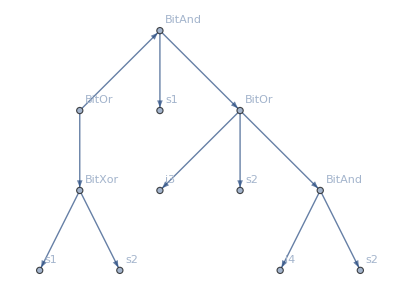
{-Graphics-,{1→Func[BitOr],2→Func[BitAnd],3→Term[s1],4→Func[BitOr],5→Term[i3],6→Term[s2],7→Func[BitAnd],8→Term[i4],9→Term[s2],10→Func[BitXor],11→Term[s1],12→Term[s2]}}

```mathematica
{g2,l2} = FunctionToGraph[f2]
```

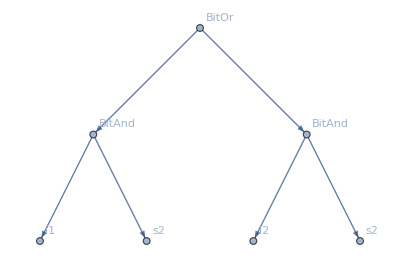
{-Graphics-,{4→Func[BitOr],5→Func[BitAnd],6→Term[i1],7→Term[s2],8→Func[BitAnd],9→Term[i2],10→Term[s2]}}

```mathematica
Subtree[g1,4,l1]
```

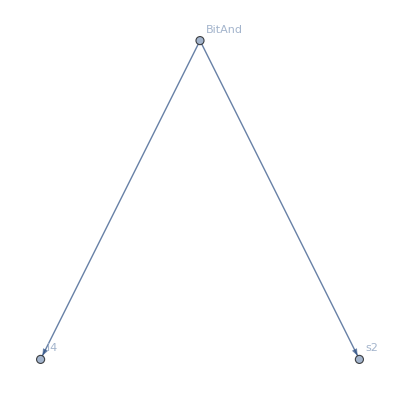
{-Graphics-,{7→Func[BitAnd],8→Term[i4],9→Term[s2]}}

```mathematica
Subtree[g2,7,l2]
```